```mathematica
dvdt1[v_,t_]=-k*v(v-a)(v-1)-v*h+S[t];
dhdt1[h_,t_] = (ε0+(µ1*h)/v+µ2)(-h-k*v(v-a-1));



(*3.1.1.a*)
S[t]=0;
dvdt1[v,t]
dhdt1[h,t]
```

-h v-k (-1+v) v (-a+v)

(-h-k v (-1-a+v)) (ε0+(h µ1)/v+µ2)

```mathematica
dvdt0=-h v-k (-1+v) v (-a+v);
```

```mathematica
dhdt0=(-h-k v (-1-a+v)) (ε0+(h µ1)/v+µ2);
dvdt0=0;
dhdt0=0;
vvalue01=(k(a+1)+Sqrt[k^2(a+1)^2-4k(k*a+h)])/(2k)
vvalue02=(k(a+1)-Sqrt[k^2(a+1)^2-4k(k*a+h)])/(2k)
hvalue01=-k*v(v-a-1)
hvalue02=(ε0(v+µ2)/µ1)
```

((1+a) k+√((1+a)^2 k^2-4 k (h+a k)))/(2 k)

((1+a) k-√((1+a)^2 k^2-4 k (h+a k)))/(2 k)

-k v (-1-a+v)

(ε0 (v+µ2))/µ1

```mathematica
(*3.1.1.b*)
vvalue03=0;
hvalue03=0;
hvalue04=-(ε0*µ2)/µ1;
```

```mathematica
(*3.1.1.c*)
gv00=ε0*k(a+1);
gh00=-ε0;
fv00=-k*a;
fh00=0;
J00=fv00*gh00-gv00*fh00
```

a k ε0

```mathematica
(*3.1.1.d*)
eigen01=fv00;
eigen02=gh00;
```

```mathematica
(*3.1.2.a*)
a=0.15;
k=8;
ε0=0.002;
µ1=0.2;
µ2=0.3;
S[t]=0;
vvalue02=t*(-h v-k (-1+v) v (-a+v))
hvalue02=t*((-h-k v (-1-a+v)) (ε0+(h µ1)/v+µ2))
hfunction[v]=v/((-h v-k (-1+v) v (-a+v)))*((-h-k v (-1-a+v)) (ε0+(h µ1)/v+µ2))
```

t (-h v-8 (-1+v) (-0.15+v) v)

t (0.302+(0.2 h)/v) (-h-8 (-1.15+v) v)

((0.302+(0.2 h)/v) v (-h-8 (-1.15+v) v))/(-h v-8 (-1+v) (-0.15+v) v)

```mathematica
nullclineVotage1=Plot[(k(a+1)+Sqrt[k^2(a+1)^2-4k(k*a+h)])/(2k),{h,-0.05,2.75},PlotRange-> {{0,1.6},{0,1}},PlotStyle->Blue];
nullclineVotage2=Plot[(k(a+1)-Sqrt[k^2(a+1)^2-4k(k*a+h)])/(2k),{h,-0.05,2.75},PlotRange-> {{0,1.6},{0,1}},PlotStyle->Blue];
nullclineVotage3=Plot[-k(v-a)(v-1),{v,-0.05,1.2},PlotStyle->Blue];
```

```mathematica
nullclineGating1=Plot[-k*v(v-a-1),{v,-0.05,1.2},PlotStyle->Red];
nullclineGating2=Plot[(ε0(v+µ2)/µ1),{v,-0.05,1.2},PlotStyle->Red];
Show[nullclineVotage3,nullclineGating1,nullclineGating2,PlotRange->{{-0.05,1.2},{-0.05,2.75}}];
```

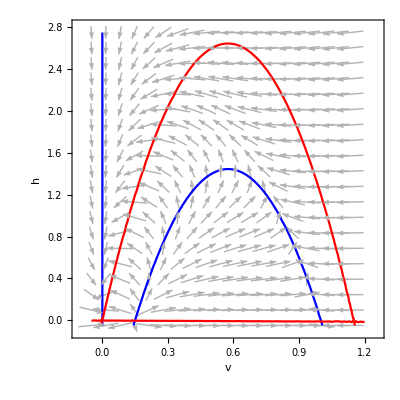

```mathematica
f[v_,h_]=-k*v(v-a)(v-1)-v*h;
g[v_,h_]=(ε0+(µ1*h)/(v+µ2))*(-h-k*v(v-a-1));
vp=VectorPlot[{f[v,h],g[v,h]},{v,-0.05,1.2},{h,-0.05,2.75},VectorScale->{0.04,0.9,None},Axes-> True, AxesLabel-> {v,h},VectorPoints->20,
VectorStyle->{GrayLevel[0.7]}

];
cp1=ContourPlot[{f[v,h]==0},{v,-0.05,1.2},{h,-0.05,2.75},ContourStyle-> Blue];
cp2=ContourPlot[{g[v,h]==0},{v,-0.05,1.2},{h,-0.05,2.75},ContourStyle-> Red];
Show[vp,cp1,cp2]
```

```mathematica
S[t]=0.25;
dvdt1[v_,t_]=-k*v(v-a)(v-1)-v*h+S[t]
dhdt1[h_,t_] = (ε0+(µ1*h)/v+µ2)(-h-k*v(v-a-1))
```

0.25-h v-8 (-1+v) (-0.15+v) v

(0.302+(0.2 h)/v) (-h-8 (-1.15+v) v)